```mathematica
ClearAll["Global`*"];
```

### Wprowadzenie hamiltonianu dla jednowymiarowego kwantowego oscylatora harmonicznego. Symbole “m”, “ℏ”, ”x” ,“ψ”oznaczają odpowiednio masę cząstki (elektronu), stałą Planka podzieloną przez liczbę 2 π , współrzędną przestrzenną (wychylenie z położenia równowagi) oraz funkcję falową cząstki. Wyrażenie “pochodna2ψ” zostanie w dalszej części programu zamienione na pochodną drugiego rzędu.

```mathematica
Hamiltonian=-ℏ^2/(2×m)×pochodna2ψ+(m×Subscript[ω, o]^2)/2×x^2×ψ;
```

### Zapisanie lewej strony równania Schrödingera “LStrSz” (prawa strona jest równa zero), przy wprowadzeniu parametrów λ = (2×En× m)/ℏ^2 oraz α = (m×ω_o)/ℏ. Symbol “En” oznacza energię oscylatora w stanie “n”.

```mathematica
LStrSz=(Hamiltonian-En×ψ)×(-2×m)/ℏ^2/.En->(λ×ℏ^2)/(2×m)/.m->(α×ℏ)/Subscript[ω, o]//Simplify
```

pochodna2ψ+(-x^2 α^2+λ) ψ

### Zdefiniowanie operatora “rown1α” jako “LStrSz” ze zmianą wyrażenia “pochodna2ψ” na pochodną drugiego rzędu funkcji falowej “ψ” względem współrzędnej “x”.

```mathematica
rown1α @ ψ_:=LStrSz/.pochodna2ψ->D[ψ, x,x]
```

### Wprowadzenie (postulowanie) rozwiązania równania Schrödingera. Niewiadomą jest funkcja “f[x]”.

```mathematica
ψ=f[x]×Exp[(-α×x^2)/2];
```

### Wygenerowanie równania różniczkowego (lewej strony, prawa jest równa zero) “rown2α” z niewiadomą funkcją “f[x]”.

```mathematica
rown2α= rown1α @ ψ //Simplify
```

ⅇ^(-(x^2 α)/2) ((-α+λ) f[x]-2 x α f'[x]+f''[x])

### Uproszczenie równania różniczkowego “rown2α” i oznaczenie jego nowej postaci jako “rown3α”.

```mathematica
rown3α=Collect[rown2α,f[x]]×ⅇ^((x^2× α)/2)//Simplify
```

(-α+λ) f[x]-2 x α f'[x]+f''[x]

### Zamiana zmiennej w równaniu “rown3α” z “x” na “ξ/(√α)”.

```mathematica
rown4α=rown3α/α/.{f[x]->f[ξ],f'[x]->√α×D[f[ξ], ξ],f''[x]->α×D[f[ξ], ξ,ξ]}/.x->ξ/(√α)//Simplify
```

(-1+λ/α) f[ξ]-2 ξ f'[ξ]+f''[ξ]

### Przekształcenie otrzymanego równania “rown4α” do równania różniczkowego Hermite’a. Wyrażenie “-1+λ/α “ zostaje zastąpione przez “2× n”, gdzie n = 0, 1, 2, 3, ... .

```mathematica
rown5α=rown4α/.(-1+λ/α)->2×n
```

2 n f[ξ]-2 ξ f'[ξ]+f''[ξ]

### Rozwiązanie otrzymanego równania różniczkowego względem niewiadomej funkcji “f[ξ]”.

```mathematica
rown6αrozw=DSolve[rown5α==0,f[ξ],ξ]
```

{{f[ξ]→C[1] HermiteH[n,ξ]+C[2] Hypergeometric1F1[-n/2,1/2,ξ^2]}}

### Zapisanie postulowanego rozwiązania równania Schrödingera jako funkcję ψξ zależna od zmiennej “ξ“.

```mathematica
ψξ=f[ξ]×Exp[(-α×x^2)/2]/.x->ξ/(√α)
```

ⅇ^(-ξ^2/2) f[ξ]

### Podstawienie fizycznego (C[2]=0) rozwiązania równania Schrödingera do funkcji falowej “ψξn” zależnej od “n”. Unormowanie funkcji falowej zapewnia przyjęcie C[1]=(2^n×n!×Sqrt[π])^(-1/2) .

```mathematica
ψξn=ψξ/.rown6αrozw[[1,1]]/.{C[1]->(2^n×n!×Sqrt[π])^(-1/2),C[2]->0}
```

(ⅇ^(-ξ^2/2) HermiteH[n,ξ])/(π^(1/4) √(2^n n!))

### Wykorzystanie równości “(-1+λ/α)=2×n” do obliczenia energii stanów własnych oscylatora “En” oraz przekształcenie otrzymanego wzoru.

```mathematica
rownEn=Solve[{α==(m×Subscript[ω, o])/ℏ,λ==(2×m×En)/ℏ^2,(-1+λ/α)==2×n},{En},{α,λ}]
```

{{En→1/2 (1+2 n) ℏ ω_o}}

```mathematica
En=En/.rownEn[[1,1]]//Expand
```

(ℏ ω_o)/2+n ℏ ω_o

```mathematica
En=Collect[En,Subscript[ω, o]×ℏ]
```

(1/2+n) ℏ ω_o

### Wypisanie wzoru na energię stanów własnych oscylatora “En”.

```mathematica
Print[StyleForm[StringForm["\n\n Energia dozwolonych stanów kwantowych dana jest wzorem:  "],FontFamily->"Times",FontSize->14,FontWeight->"Bold",FontSlant->"Plain"]]

Print[StyleForm[StringForm["   En = `` \n\n ",En],FontFamily->"Times",FontSize->14,FontWeight->"Bold",FontSlant->"Plain",FontColor->Gray]]
```

Energia dozwolonych stanów kwantowych dana jest wzorem:

En = (1/2+n) ℏ ω_o

### Sporządzenie wykresu przedstawiającego pierwsze cztery poziomy energetyczne (n = 0, 1, 2, 3), odpowiadające im funkcje falowe “ψ[ξ, n]”oraz zależność energii potencjalnej “Ep[ξ]”oscylatora od współrzędnej “ξ”.

```mathematica
wykresy[ωo_]:=Module[{Enstyle={Gray,Thickness[0.002],Dashed},psistyle={Gray},ℏ=1.055×10^-34,EneV=1.6×10^-19},Plot[{ξ^2×(ℏ×ωo)/2/EneV,1/2 ×ℏ ×ωo/EneV,3/2 ×ℏ ×ωo/EneV,5/2 ×ℏ ×ωo/EneV,7/2 ×ℏ ×ωo/EneV,1/2 ×ℏ ×ωo/EneV+15×ψξn/.n->0,3/2 ×ℏ ×ωo/EneV+15×ψξn/.n->1,5/2 ×ℏ ×ωo/EneV+15×ψξn/.n->2,7/2 ×ℏ ×ωo/EneV+15×ψξn/.n->3},{ξ,-4.5,4.5},PlotStyle->{Black,Enstyle,Enstyle,Enstyle,Enstyle,psistyle,psistyle,psistyle,psistyle},PlotRange->{Automatic,{0,100}},AxesLabel->{"ξ, 1", "En, eV"},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotLabels->Placed[{None,"1/2ℏω_o","3/2ℏω_o","5/2ℏω_o","7/2ℏω_o","ψ[ξ,n=0]","ψ[ξ,n=1]","ψ[ξ,n=2]","ψ[ξ,n=3]"},{None,Before,Before,Before,Before,After,After,After,After}],PlotLegends->{"Ep[ξ]"}]]
```

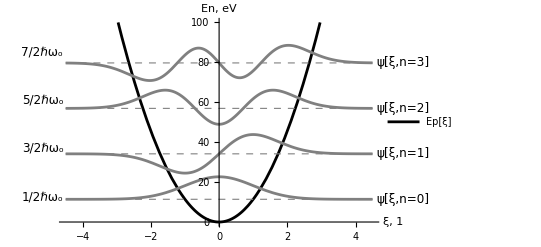

```mathematica
wykresy[2×3.14×5.5×10^15]
```

### Wprowadzenie funkcji “ψξl” zależnej od “l”.

```mathematica
ψξl=ψξn/.n->l
```

(ⅇ^(-ξ^2/2) HermiteH[l,ξ])/(π^(1/4) √(2^l l!))

### Przedstawienie hamiltonianu w funkcji zmiennej “ξ”.

```mathematica
Hamiltonianξ  @ ψξ_ := Hamiltonian /.{pochodna2ψ->α×D[ψξ, ξ,ξ],x^2×ψ->ξ^2/α×ψξ}/.α->(m×Subscript[ω, o])/ℏ
```

### Wygenerowanie postaci macierzowej hamiltonianu “macierzH” w bazie jego funkcji własnych ψξl.

```mathematica
calka[n1_,l1_]:=(n=n1; l=l1;Integrate[ψξn×Hamiltonianξ @ ψξl,{ξ,-∞,+∞}])
```

```mathematica
macierzH=Table[calka[i,j],{i,0,3},{j,0,3}]
```

{{(ℏ ω_o)/2,0,0,0},{0,(3 ℏ ω_o)/2,0,0},{0,0,(5 ℏ ω_o)/2,0},{0,0,0,(7 ℏ ω_o)/2}}

```mathematica
MatrixForm[macierzH]
```

((ℏ ω_o)/2 | 0 | 0 | 0
0 | (3 ℏ ω_o)/2 | 0 | 0
0 | 0 | (5 ℏ ω_o)/2 | 0
0 | 0 | 0 | (7 ℏ ω_o)/2)

### Rozwiązanie zagadnienia wartości własnych i wektorów własnych macierzy hamiltonianu .

```mathematica
Eigensystem[macierzH]//MatrixForm
```

((7 ℏ ω_o)/2 | (5 ℏ ω_o)/2 | (3 ℏ ω_o)/2 | (ℏ ω_o)/2
{0,0,0,1} | {0,0,1,0} | {0,1,0,0} | {1,0,0,0})

### Obliczenia wartości własnych hamiltonianu (w eV) dla ω_o=2×3.14×5.5×10^15 rad/s.

```mathematica
MatrixForm[macierzH]/.{Subscript[ω, o]->2×π×5.5×10^15,ℏ->1.055×10^-34/(1.6×10^-19)}
```

(11.3932 | 0 | 0 | 0
0 | 34.1795 | 0 | 0
0 | 0 | 56.9659 | 0
0 | 0 | 0 | 79.7523)